# SSH model

## Bulk band structure (periodic boundary conditions)

Here tp is actually t’/t as we measure all energies in units of t (throughout this Mathematica notebook).

```mathematica
Manipulate[Plot[{-Abs[1+tp Exp[I k]],Abs[1+tp Exp[I k]]},{k,-π,π},PlotRange->{-2.9,2.9},PlotStyle->Directive[Thick, Red],ImageSize->500,LabelStyle->20,Frame->True,FrameStyle->Thick],{tp,0,2.5}]
```

## Finite system with open boundary conditions (i.e., two edges)

Let’s set up the Hamiltonian for Ns sites:

```mathematica
Ham[tp_,Ns_]:=SparseArray[{Band[{1,2},Automatic,{2,2}]->1,Band[{2,1},Automatic,{2,2}]->1,Band[{2,3},Automatic,{2,2}]->tp,Band[{3,2},Automatic,{2,2}]->tp},{2Ns,2Ns}];
(*Ham[tp,5]//MatrixForm*)
```

```mathematica
EVs[tp_?NumericQ,Np_]:=Sort[Eigenvalues[Ham[N[tp],Np]],#1<#2&]
```

Plot as a function of t’:

```mathematica
DATA=Table[EVs[tp,40],{tp,0,2,0.1}];
```

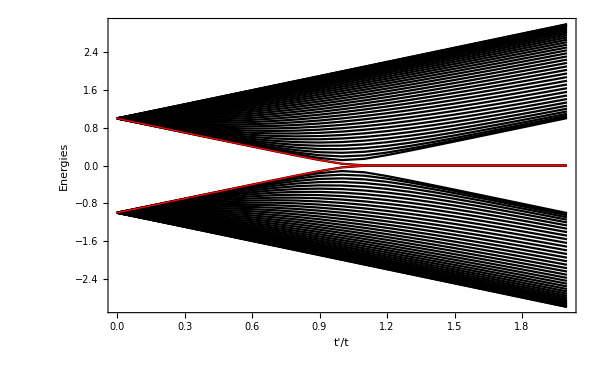

```mathematica
Show[ListPlot[Transpose[DATA],PlotStyle->Directive[Black],Joined->True,DataRange->{0,2},Frame->True,FrameStyle->Thick,LabelStyle->20,ImageSize->600,FrameLabel->{"t'/t","Energies"}],ListPlot[Transpose[DATA][[40;;41]],PlotStyle->Directive[Red,Thick],Joined->True,DataRange->{0,2}]]
```

Almost-zero-energy states in the topological phase as a function of system size:

```mathematica
DATA=Table[{Ns,EVs[1.4,Ns][[Ns+1]]},{Ns,10,60,1}]//Quiet;
```

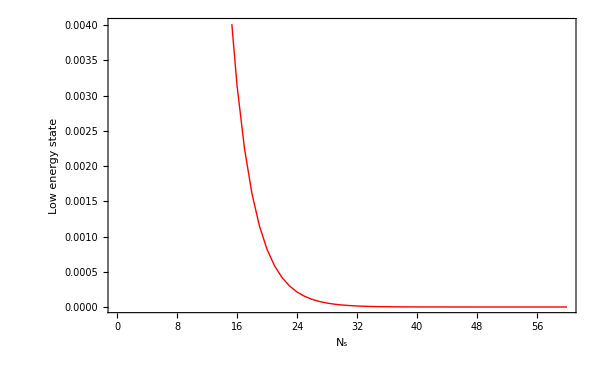

```mathematica
ListPlot[DATA,Joined->True,DataRange->{0,2},Frame->True,PlotStyle->Directive[Thick,Red],FrameStyle->Directive[Thick,Black],LabelStyle->20,ImageSize->600,FrameLabel->{"N_s","Low energy state"}]
```

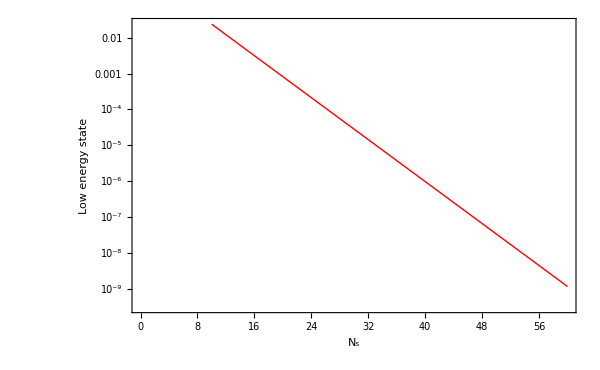

```mathematica
ListLogPlot[DATA,Joined->True,DataRange->{0,2},Frame->True,PlotStyle->Directive[Thick,Red],FrameStyle->Directive[Thick,Black],LabelStyle->20,ImageSize->600,FrameLabel->{"N_s","Low energy state"}]
```